```mathematica
nt=20;
xtable=Table[x/.FindRoot[LegendreP[nt, x]==0, {x, -Cos[π(j-0.25)/(nt+0.5)]}], {j, 1, nt}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

{-0.993129,-0.963972,-0.912234,-0.839117,-0.746332,-0.636054,-0.510867,-0.373706,-0.227786,-0.0765265,0.0765265,0.227786,0.373706,0.510867,0.636054,0.746332,0.839117,0.912234,0.963972,0.993129}

```mathematica
np=20;
phitable=N[Table[2π k/np, {k, 0, np-1}]]
```

{0.,0.314159,0.628319,0.942478,1.25664,1.5708,1.88496,2.19911,2.51327,2.82743,3.14159,3.45575,3.76991,4.08407,4.39823,4.71239,5.02655,5.34071,5.65487,5.96903}

```mathematica
xitable
```

xitable

```mathematica
B[θ_, ϕ_]:=10SphericalHarmonicY[0,0,θ,ϕ]+1SphericalHarmonicY[1,0,θ,ϕ]+2Im[SphericalHarmonicY[2,1,θ,ϕ]]
```

```mathematica
B2[θ_, ϕ_]:=10SphericalHarmonicY[0,0,θ,ϕ]-2Re[SphericalHarmonicY[2,0,θ,ϕ]]+0.5Re[SphericalHarmonicY[4,0,θ,ϕ]]
SphericalPlot3D[B2[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->0]
```

-Graphics3D-

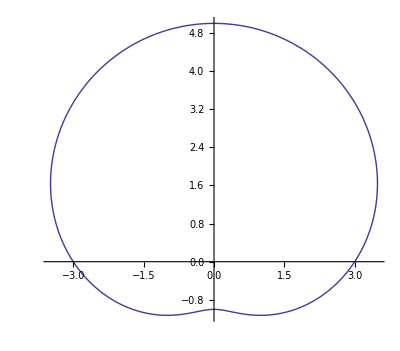

```mathematica
PolarPlot[3+2Cos[θ-π/2], {θ, 0, 2π}]
```

```mathematica
B3[θ_, ϕ_]:=3+2θ ϕ
SphericalPlot3D[B3[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->0]
```

-Graphics3D-

```mathematica
B[ArcCos[0.7415311855993943], 4.487989505128276]
```

3.93269

```mathematica
B[ArcCos[xtable⟦1⟧], phitable⟦1⟧]
```

2.35721

```mathematica
Table[B[ArcCos[xtable⟦j⟧], phitable⟦k⟧], {j, 1, nt}, {k, 1, np}]//TableForm
```

2.35721 | 2.71831 | 2.8075 | 2.55761 | 2.15682 | 1.90693 | 1.99611
2.45863 | 3.05962 | 3.20806 | 2.79216 | 2.12511 | 1.70921 | 1.85764
2.62265 | 3.07072 | 3.18139 | 2.87131 | 2.37399 | 2.06391 | 2.17458
2.82095 | 2.82095 | 2.82095 | 2.82095 | 2.82095 | 2.82095 | 2.82095
3.01924 | 2.57117 | 2.46051 | 2.77058 | 3.26791 | 3.57798 | 3.46732
3.18326 | 2.58227 | 2.43384 | 2.84974 | 3.51679 | 3.93269 | 3.78425
3.28468 | 2.92358 | 2.8344 | 3.08429 | 3.48508 | 3.73497 | 3.64578

```mathematica
plot1=SphericalPlot3D[B[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

```mathematica
plot3=SphericalPlot3D[1, {θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

```mathematica
gridlist=Flatten[Table[{Sin[ArcCos[xtable⟦j⟧]]Cos[phitable⟦k⟧], Sin[ArcCos[xtable⟦j⟧]]Sin[phitable⟦k⟧], Cos[ArcCos[xtable⟦j⟧]]}, {j, 1, nt}, {k, 1, np}], 1];
```

```mathematica
plot4=ListPointPlot3D[gridlist]
```

-Graphics3D-

```mathematica
Show[plot3, plot4]
```

-Graphics3D-

```mathematica
boundlist=Flatten[Table[{B[ArcCos[xtable⟦j⟧], phitable⟦k⟧]Sin[ArcCos[xtable⟦j⟧]]Cos[phitable⟦k⟧], B[ArcCos[xtable⟦j⟧], phitable⟦k⟧]Sin[ArcCos[xtable⟦j⟧]]Sin[phitable⟦k⟧], B[ArcCos[xtable⟦j⟧], phitable⟦k⟧]Cos[ArcCos[xtable⟦j⟧]]}, {j, 1, nt}, {k, 1, np}], 1];
```

```mathematica
plot2=ListPointPlot3D[boundlist]
```

-Graphics3D-

```mathematica
Show[plot1, plot2]
```

-Graphics3D-